## Maximum Mass

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/GitHub/compactobjects/neutronStarModel/resource

```mathematica
xi[chi_]=6Cos[chi]/(9Cos[chi]-2Sin[chi]^3/(chi-Sin[chi]Cos[chi]))-1
```

-1+(6 Cos[chi])/(9 Cos[chi]-(2 Sin[chi]^3)/(chi-Cos[chi] Sin[chi]))

```mathematica
main=Plot[xi[chi],{chi,0,Pi},FrameLabel->Style["ξ(χ)",20],PlotRange->{Automatic,{-2,2}},Frame->True,ImageSize->800];sub1=Plot[{9 Cos[chi],(2 Sin[chi]^3)/(chi-Cos[chi] Sin[chi])},{chi,0,Pi/2},ImageSize->400,Frame->True,FrameLabel->Style["Two Terms in Denominator",20]];
sub2=Plot[{chi,Sin[chi]Cos[chi]},{chi,0,Pi/2},ImageSize->400,Frame->True,FrameLabel->Style["χ, sinχcosχ",20]];
```

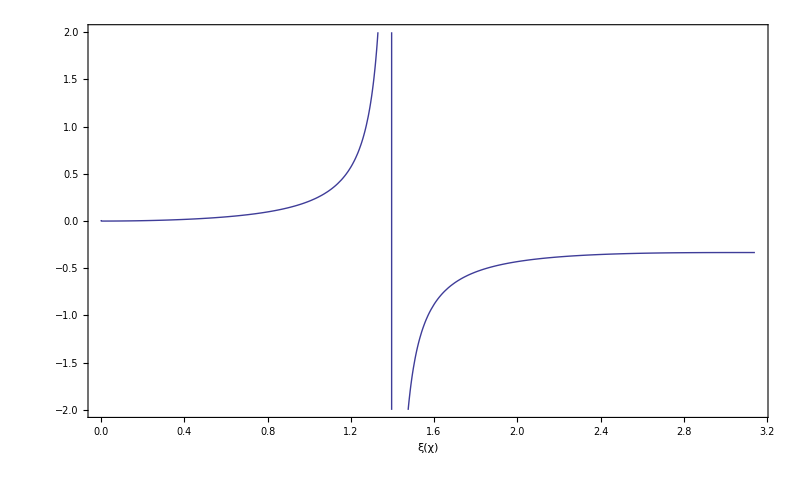
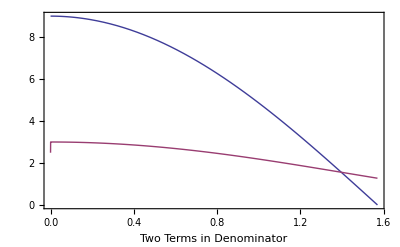
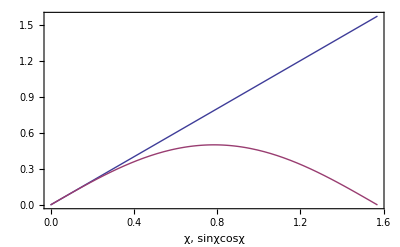
-Graphics- | 
-Graphics- | -Graphics-

xiChi.png

```mathematica
all=Grid[{{main,SpanFromLeft},{sub1,sub2}}]
Export["xiChi.png",all]
```